```mathematica
ClearAll["Global`*"];
(*W dolnym punkcie wykonywanej w płaszczyźnie pionowej pętli samolot
porusza się z prędkością 1100 km/h. Sporządzić wykres zależności stosunku
siły odśrodkowej działającej na lotnika do siły ciężkości od promienia pętli r, dla r=0.9÷1.5 km. Przyjmując następnie,że promień pętli r=1 km, znaleźć stosunek siły odśrodkowej do siły ciężkości działającej na lotnika,jeżeli prędkość samolotu w dolnym punkcie wynosi v. Sporządzić wykres dla
v=800÷1200 km/h. *)
```

```mathematica
g=9.81;          (* m/s^2 *)
```

```mathematica
Fd=(m×v^2)/r;
Fg=m×g;
```

```mathematica
stos=Fd/Fg;
```

```mathematica
stos1=Fd/Fg/.v->1100×10^3/3600;
```

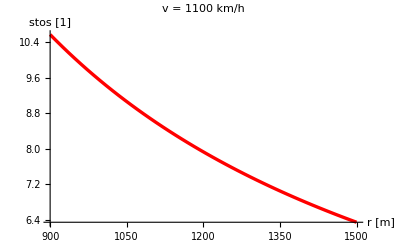

```mathematica
rys1=Plot[stos1,{r,900,1500},BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
PlotLabel->StyleForm["      v = 1100 km/h     ",FontFamily->"Helvetica",FontSlant->"Plain",FontWeight->"Bold",FontSize->12],
PlotStyle->({{RGBColor[1,0,0], Thickness[0.006]}}),AxesLabel->{"r [m] ","stos [1]"}]
```

```mathematica
r=1000;       (* m *)
```

```mathematica
vmin=800×10^3/3600;
vmax=1200×10^3/3600;
```

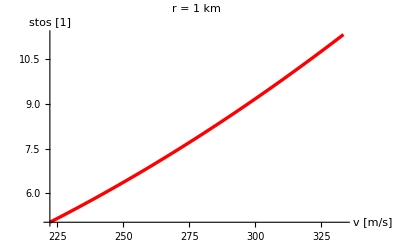

```mathematica
rys1=Plot[stos,{v,vmin,vmax},BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
PlotLabel->StyleForm["      r = 1 km     ",FontFamily->"Helvetica",FontSlant->"Plain",FontWeight->"Bold",FontSize->12],
PlotStyle->({{RGBColor[1,0,0], Thickness[0.006]}}),AxesLabel->{"v [m/s] ","stos [1]"}]
```